## Convergencia Mie-CST

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Paquetes a importar

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\3-FIT"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\3-FIT

```mathematica
(*SetDirectory[NotebookDirectory[]];*)
(*Needs["MieTheory`"]*)
```

```mathematica
<< "MieTheory.wl"
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
colors2={blueUNAM, redUNAM}
color5={Orange}
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
rojos=Table[RGBColor[1,g,0],{g,0,0.9,0.16}]
sunsetColors=Table[ColorData["SunsetColors"][i],{i,0,0.8,1/7}]
```

{RGBColor[Rational[2, 85], Rational[151, 255], Rational[71, 85]],RGBColor[Rational[232, 255], Rational[4, 15], Rational[14, 85]]}

{RGBColor[1, 0.5, 0]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[1, 0., 0],RGBColor[1, 0.16, 0],RGBColor[1, 0.32, 0],RGBColor[1, 0.48, 0],RGBColor[1, 0.64, 0],RGBColor[1, 0.8, 0]}

{RGBColor[0., 0., 0.],RGBColor[0.3195368571428571, 0.1164, 0.4341454285714286],RGBColor[0.6695744285714286, 0.22438285714285713, 0.338128],RGBColor[0.8974812857142858, 0.3693308571428571, 0.1452665142857143],RGBColor[0.9882154285714286, 0.5505617142857143, 0.08483494285714285],RGBColor[1., 0.7397017142857143, 0.23300614285714283]}

## Funciones

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]

errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]

errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> sunsetColors,
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10"},
   ImagePadding->{{90,10},{60,60}}};
```

## Índice de refracción usado en CST

```mathematica
datosIM=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas\\CST\\epsEritrocitosData30_Im_Fit.csv"];
datosRE=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas\\CST\\epsEritrocitosData30_Re_Fit.csv"];

(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
parteImFit=Interpolation[Transpose[{datosIM[[All,1]],datosIM[[All,2]]}]];
parteReFit=Interpolation[Transpose[{datosRE[[All,1]],datosRE[[All,2]]}]];

nindexEriFit[lambda_]:=Sqrt[parteReFit[lambda]+I*parteImFit[lambda]]
```

## Convergencia

### Mie

```mathematica
eriQabsMie=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQscaMie=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
```

### Matriz

```mathematica
dataMatrizCabs=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Matriz_Cabs.csv"];
dataMatrizCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Matriz_Csca.csv"];

dataQabsMatriz=Transpose[{dataMatrizCabs[[All,1]],dataMatrizCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,7];
dataQscaMatriz=Transpose[{dataMatrizCsca[[All,1]],dataMatrizCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,7];
```

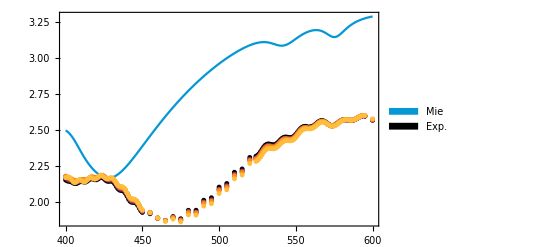

```mathematica
interpMatriz=ListPlot[eriQextMie,PlotStyle->blueUNAM,
              PlotLegends->Placed[SwatchLegend[{Style["Mie",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
              Joined->True,
              Evaluate[Sequence @@ plotStyling]];
plotpointsMatriz=ListPlot[dataQext[dataQabsMatriz[[#]],dataQscaMatriz[[#]]]&/@Range[1,6],PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                    LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                                    Evaluate[Sequence @@ plotStyling]];

ajusteMatriz=Show[{interpMatriz,plotpointsMatriz}, FrameLabel->{{Style[MaTeX["\\varepsilon''(\\lambda) "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicks28}},
                                PlotRange->All]
```

### Mallado global

### Mallado local - Superficie

### Mallado local - Volumen